# MWE : Extrusion

## Take a 2D shape and make it 3D:

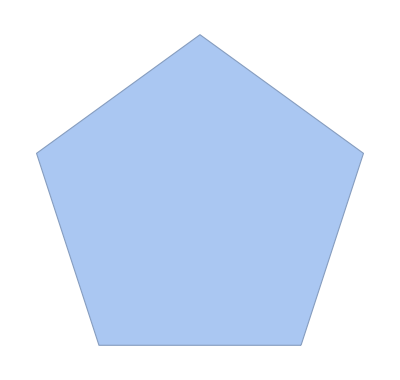

```mathematica
shape=DiscretizeGraphics@RegularPolygon[5]
```

```mathematica
RegionProduct[shape,Line[{{0.},{1.}}]]
```

-Graphics3D-

## Extrusion along a curve

There is a good discussion about extrusion along curves on StackExchange:
https://mathematica.stackexchange.com/questions/3051/extruding-along-a-path